```mathematica
(*Network Parameters, M = Network Size, T = Total Time Steps*)
M=20;
T =80;

(*Create empty qubit states*)
QMVecs = {};
CLVecs = {};
vec = Table[0,{2*M}];
vec[[1]] = 1;
vec2 = Table[0,{2*M}];
vec2[[1]] = 1;
QMVecs = Append[QMVecs,vec[[Table[j,{j,1,M}]]]];
CLVecs = Append[CLVecs,vec2[[Table[j,{j,1,M}]]]] ;
QMVecs = Append[QMVecs,vec[[Table[j,{j,M+1,2*M}]]]];
CLVecs = Append[CLVecs,vec2[[Table[j,{j,M+1,2*M}]]]] ;

(*Create Truth Functions and the Wiring*)

TTs = {};
Wiring = {};
Wiring = Append[Wiring, Table[j,{j,M+1,2*M-1}]];
Wiring = Flatten[Prepend[Wiring, {2*M}]];
For[i =1 , i ≤ M,i++,
TTs = Append[TTs, {-1,1}];
];
hamDT = {};
hamDT2 = {};

(*Calculate the Evolution of the hamming distance
for the classical and quantum case*)
For[t =1, t≤ T,t++,
For[i=1, i≤ M,i++,
If[i ≤ 15,
Switch[vec[[i]],1,vec[[i]] = 3; , 3,  vec[[i]] = 1;];
];
If[TTs[[M+1-i]][[1]]  == -1,
(*QM*)
Switch[{vec[[i]],vec[[Wiring[[i]]]]},
{0,1},vec[[i]] = 1; vec[[Wiring[[i]]]]=1; ,
{1,1},vec[[i]] = 0; vec[[Wiring[[i]]]]=1; ,
{3,0},vec[[i]] = 3; vec[[Wiring[[i]]]]=3; ,
{3,3},vec[[i]] = 3; vec[[Wiring[[i]]]]=0; ,
{3,1},vec[[i]] = 2; vec[[Wiring[[i]]]]=2; ,
{2,2},vec[[i]] = 3; vec[[Wiring[[i]]]]=1; ,
{2,1},vec[[i]] = 3; vec[[Wiring[[i]]]]=2; ,
{3,2},vec[[i]] = 2; vec[[Wiring[[i]]]]=1; ,
{1,2},vec[[i]] = 0; vec[[Wiring[[i]]]]=2; ,
{0,2},vec[[i]] = 1; vec[[Wiring[[i]]]]=2; ,
{2,0},vec[[i]] = 2; vec[[Wiring[[i]]]]=3; ,
{2,3},vec[[i]] = 2; vec[[Wiring[[i]]]]=0;
];,
(*Classic*)
Switch[{vec2[[i]],vec2[[Wiring[[i]]]]},
{0,1},vec2[[i]] = 1; vec2[[Wiring[[i]]]]=1; ,
{1,1},vec2[[i]] = 0; vec2[[Wiring[[i]]]]=1; ,
{3,0},vec2[[i]] = 3; vec2[[Wiring[[i]]]]=3; ,
{3,3},vec2[[i]] = 3; vec2[[Wiring[[i]]]]=0; ,
{3,1},vec2[[i]] = 2; vec2[[Wiring[[i]]]]=2; ,
{2,2},vec2[[i]] = 3; vec2[[Wiring[[i]]]]=1; ,
{2,1},vec2[[i]] = 3; vec2[[Wiring[[i]]]]=2; ,
{3,2},vec2[[i]] = 2; vec2[[Wiring[[i]]]]=1; ,
{1,2},vec2[[i]] = 0; vec2[[Wiring[[i]]]]=2; ,
{0,2},vec2[[i]] = 1; vec2[[Wiring[[i]]]]=2; ,
{2,0},vec2[[i]] = 2; vec2[[Wiring[[i]]]]=3; ,
{2,3},vec2[[i]] = 2; vec2[[Wiring[[i]]]]=0; 
];
];
If[TTs[[M+1-i]][[2]]  == -1,
(*QM*)
Switch[{vec[[i]],vec[[Wiring[[i]]]]},
{0,1},vec[[i]] = 1; vec[[Wiring[[i]]]]=1; ,
{1,1},vec[[i]] = 0; vec[[Wiring[[i]]]]=1; ,
{3,0},vec[[i]] = 3; vec[[Wiring[[i]]]]=3; ,
{3,3},vec[[i]] = 3; vec[[Wiring[[i]]]]=0; ,
{3,1},vec[[i]] = 2; vec[[Wiring[[i]]]]=2; ,
{2,2},vec[[i]] = 3; vec[[Wiring[[i]]]]=1; ,
{2,1},vec[[i]] = 3; vec[[Wiring[[i]]]]=2; ,
{3,2},vec[[i]] = 2; vec[[Wiring[[i]]]]=1; ,
{1,2},vec[[i]] = 0; vec[[Wiring[[i]]]]=2; ,
{0,2},vec[[i]] = 1; vec[[Wiring[[i]]]]=2; ,
{2,0},vec[[i]] = 2; vec[[Wiring[[i]]]]=3; ,
{2,3},vec[[i]] = 2; vec[[Wiring[[i]]]]=0; 
];,
(*Classic*)
Switch[{vec2[[i]],vec2[[Wiring[[i]]]]},
{0,1},vec2[[i]] = 1; vec2[[Wiring[[i]]]]=1; ,
{1,1},vec2[[i]] = 0; vec2[[Wiring[[i]]]]=1; ,
{3,0},vec2[[i]] = 3; vec2[[Wiring[[i]]]]=3; ,
{3,3},vec2[[i]] = 3; vec2[[Wiring[[i]]]]=0; ,
{3,1},vec2[[i]] = 2; vec2[[Wiring[[i]]]]=2; ,
{2,2},vec2[[i]] = 3; vec2[[Wiring[[i]]]]=1; ,
{2,1},vec2[[i]] = 3; vec2[[Wiring[[i]]]]=2; ,
{3,2},vec2[[i]] = 2; vec2[[Wiring[[i]]]]=1; ,
{1,2},vec2[[i]] = 0; vec2[[Wiring[[i]]]]=2; ,
{0,2},vec2[[i]] = 1; vec2[[Wiring[[i]]]]=2; ,
{2,0},vec2[[i]] = 2; vec2[[Wiring[[i]]]]=3; ,
{2,3},vec2[[i]] = 2; vec2[[Wiring[[i]]]]=0; 
];
];
];
(*Apply the swap operations*)
temp = {};
temp = vec[[Table[j,{j,M+1,2*M}]]];
vec[[Table[j,{j,M+1,2*M}]]] = vec[[Table[j,{j,1,M}]]];
vec[[Table[j,{j,1,M}]]] = temp;
temp = {};
temp = vec2[[Table[j,{j,M+1,2*M}]]];
vec2[[Table[j,{j,M+1,2*M}]]] = vec2[[Table[j,{j,1,M}]]];
vec2[[Table[j,{j,1,M}]]] = temp;

vecT = vec[[Table[j,{j,1,Length[vec]/2}]]];
vec2T = vec2[[Table[j,{j,1,Length[vec2]/2}]]];

(*QMVecs = Append[QMVecs,vec[[Table[j,{j,M+1,2*M}]]]];
CLVecs = Append[CLVecs,vec2[[Table[j,{j,M+1,2*M}]]]] ;*)
QMVecs = Append[QMVecs,vecT];
CLVecs = Append[CLVecs,vec2T] ;
];

(*Calculate the total hamming distance*)

HDQM = {};
For[i = 1, i ≤Length[QMVecs],i++,
HDQM = Append[HDQM,Count[QMVecs[[i]],1]+Count[QMVecs[[i]],2]+Count[QMVecs[[i]],3]];
]
HDCL= {};
For[i = 1, i ≤Length[CLVecs],i++,
HDCL = Append[HDCL,Count[CLVecs[[i]],1]+Count[CLVecs[[i]],2]+Count[CLVecs[[i]],3]];
]
net = {};
For[i = 1, i ≤ M, i++,
net= Append[net, (Wiring[[i]]-M)->i]];
```

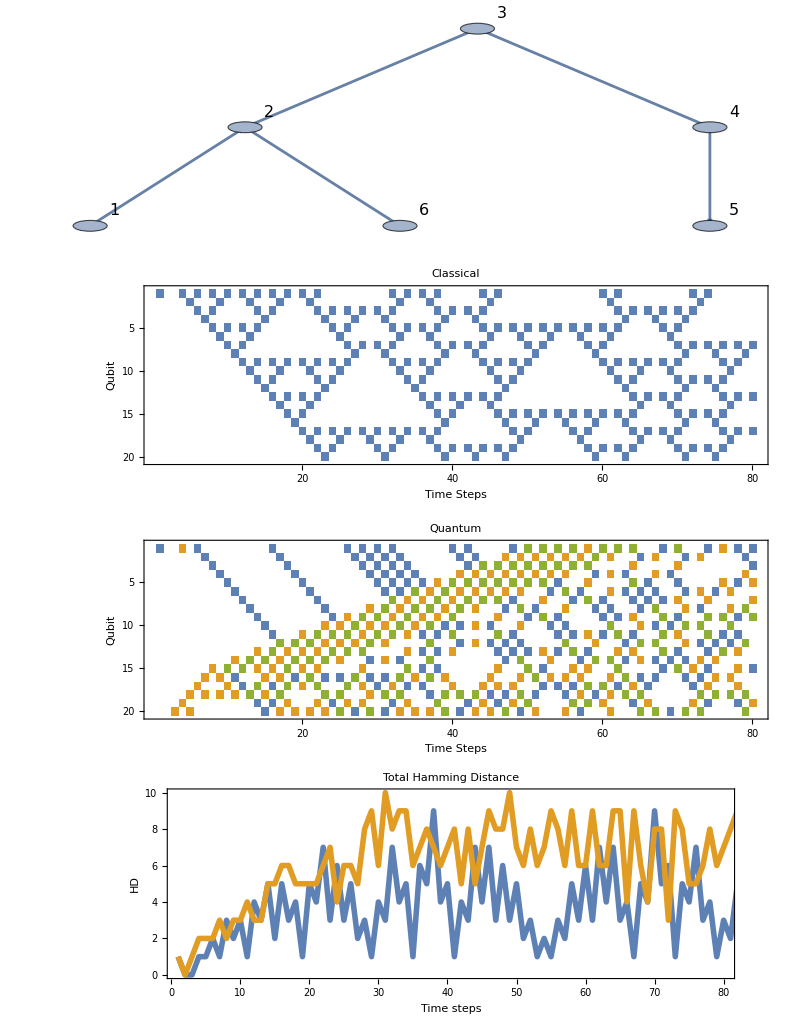

```mathematica
(*Plot the results*)

fl = {{"Time Steps",None},{"Qubit",None}};
fl2= {{" ", None},{None,None}};
fl3= {{"Time Steps",None},{None,None}};
fl4= {{"Time Steps",None},{"Qubit",None}};
fs = 16;
fs2 = 24;
ls = {FontFamily->"CMU Serif",FontSize->fs};
ft= {{Automatic,None},{Automatic,None}};
ft2 = {{{1,3,5},None},{Automatic,None}};
cr = {1->ColorData[97,"ColorList"][[1]],2-> ColorData[97,"ColorList"][[3]],3-> ColorData[97,"ColorList"][[2]],0->White};
pr = {{1,M},{1,T}};
pr2= {{1,T},Automatic};

p1 =Graph[{1->2,2->3,3->4,4->5,2-> 6},VertexLabels->"Name",EdgeStyle->Thickness[.005],VertexSize-> .11,VertexLabelStyle->Directive[Black,FontFamily->"CMU Serif",fs],EdgeShapeFunction->GraphElementData[{"Arrow","ArrowSize"->.05}]];
p2= MatrixPlot[Transpose[CLVecs],Frame->True,LabelStyle->ls,PlotLabel->Style["Classical",FontSize-> fs2,Bold],FrameLabel->fl,LabelStyle->{20},ColorRules->cr,ImageSize->1100, PlotRange->pr,AspectRatio->.3,FrameTicks->ft,PlotRange->pr];
p3=MatrixPlot[Transpose[QMVecs],Frame->True,LabelStyle->ls,PlotLabel->Style["Quantum",FontSize-> fs2,Bold],FrameLabel->fl,LabelStyle->{20},ColorRules->cr,ImageSize->1100, PlotRange->pr,AspectRatio->.3,FrameTicks->ft,PlotRange->pr];
p4=ListLinePlot[{HDCL,HDQM},Joined->True,Frame->True,LabelStyle->ls,FrameLabel->{{"HD",None},{"Time steps",None}},PlotStyle->Thickness[.004],LabelStyle->{20},ImageSize->1000,AspectRatio->.35,FrameTicks->Automatic,PlotRange->pr2,PlotLabel->Style["Total Hamming Distance",FontSize-> fs2,Bold]];
GraphicsColumn[{p1,p2,p3,p4},Spacings->{-10,0},ImageSize->800]
```